This Notebook is made only for cases near tunnelling-without-barrier scenarios, that is, ω+2ω fields with π/2 phase shift and equal intensities.

## Configurations and Equations

### Field Configuration

#### Unit conversions

```mathematica
λToω[λ_]:=2π (0.052918 ×137)/λ
```

```mathematica
ωToλ[ω_]:=2π (0.052918 ×137)/ω
```

#### fieldConfig struct

```mathematica
fieldConfig::usage = "fieldConfig[] is a protected variable, which will act to hold an association of all its defining components, e.g., the time-dependence, wavelength, intensity";
Protect[fieldConfig];
(*this is the container (struct) where I can put all the field information into*)
```

```mathematica
E1
```

E1

```mathematica
fcSymbolic=fieldConfig["E1"->E1,"E2"->E2,"E0"->E0, "ϕ1"->ϕ1,"ϕ2"->ϕ2,"r"->1,"s"->2,"ω"->ω,"p"->4,"E3"->E3];
fcSymbolicToStrings={E1->"E1",E2->"E2",E0->"E0",ϕ1->"ϕ1",ϕ2->"ϕ2",ω->"ω",E3->"E3"};
```

#### TWOBfcSymbolic (the tunnelling without barrier scenario)

```mathematica
TWOBfcSymbolic=makeFieldConfig["θ"->π/4,
"E0"->E0,
"ϕ1"->π/2,"ϕ2"->-π/2,
"r"->1,"s"->2, "p"->4,
"ω"->ω]
```

makeFieldConfig[θ→π/4,E0→E0,ϕ1→π/2,ϕ2→-π/2,r→1,s→2,p→4,ω→ω]

#### makeFieldConfig

```mathematica
makeFieldConfig["E1"->E1_,"E2"->E2_,"E0"->E0_,"ϕ1"->ϕ1_,"ϕ2"->ϕ2_,"r"->r_,"s"->s_,"ω"->ω_,"E3"->E3_,"p"->p_]:=fieldConfig[
"E1"->E1,
"E2"->E2,
"E0"->E0,
"E3"->E3,
"ϕ1"->ϕ1,"ϕ2"->ϕ2,
"r"->r,"s"->s,"p"->p,
"ω"->ω]
(* this shall generate a fieldConfig that can then be used for further computation of the field, the potential, the action etc. *)
```

I can overload this with a lot of definitions, e.g. income intensity etc.

```mathematica
makeFieldConfig["θ"->θ_,"E0"->E0_,"ϕ1"->ϕ1_,"ϕ2"->ϕ2_,"r"->r_,"s"->s_,"ω"->ω_,"p"->p_]:=fieldConfig[
"E1"->Cos[θ]E0,
"E2"->Sin[θ]E0,
"E3"->0.01E0,
"E0"->E0,
"ϕ1"->ϕ1,"ϕ2"->ϕ2,
"r"->r,"s"->s,"p"->p,
"ω"->ω]
```

```mathematica
makeFieldConfig["θ"->θ_,"E0"->E0_,"ϕ1"->ϕ1_,"ϕ2"->ϕ2_,"r"->r_,"s"->s_,"ω"->ω_,"p"->p_,"E3percent"->E3percent_]:=fieldConfig[
"E1"->Cos[θ]E0,
"E2"->Sin[θ]E0,
"E3"->E3percent E0,
"E0"->E0,
"ϕ1"->ϕ1,"ϕ2"->ϕ2,
"r"->r,"s"->s,"p"->p,
"ω"->ω]
```

A tunnelling-without-barrier scenario will (at least for now) always be this:

```mathematica
makeTWOBFieldConfig["E0"->E0_,"ω"->ω_]:=makeFieldConfig["θ"->π/4,
"E0"->E0,
"ϕ1"->π/2,"ϕ2"->-π/2,
"r"->1,"s"->2,"p"->0,
"ω"->ω]
```

#### test configuration

```mathematica
(*testfieldconfig=makeFieldConfig["θ"->π/4,
"E0"->Sqrt[4×10^14/(3.5×10^16)],
"ϕ1"->π/2,"ϕ2"->-π/2,
"r"->1,"s"->2,
"ω"->λToω[800],
"p"->0]*)
test2fieldconfig=makeFieldConfig["θ"->π/4,
"E0"->Sqrt[4×10^14/(3.5×10^16)],
"ϕ1"->π/2,"ϕ2"->-π/2,
"r"->1,"s"->2,
"ω"->λToω[800],
"p"->4,"E3"->0.01]
```

makeFieldConfig[θ→π/4,E0→0.106904,ϕ1→π/2,ϕ2→-π/2,r→1,s→2,ω→0.0569395,p→4,E3→0.01]

```mathematica
testfieldconfigNo3=makeFieldConfig["θ"->π/4,
"E0"->Sqrt[4×10^14/(3.5×10^16)],
"ϕ1"->π/2,"ϕ2"->-π/2,
"r"->1,"s"->2,
"ω"->λToω[800],
"p"->4,"E3percent"->0.2]
```

fieldConfig[E1→0.0755929,E2→0.0755929,E3→0.0213809,E0→0.106904,ϕ1→π/2,ϕ2→-π/2,r→1,s→2,p→4,ω→0.0569395]

```mathematica
field2fromConfig[test2fieldconfig][ωt]
```

0.01 Cos[4 ωt]

```mathematica
0.0010690449676496977 Cos[4 ωt]
```

0.00106904 Cos[4 ωt]

```mathematica
fieldFromConfig[test2fieldconfig][ωt]
```

0.00808122 Cos[ωt]-0.00808122 Cos[2 ωt]

```mathematica
fieldFromConfig[testfieldconfigNo3][ωt]
```

0.0755929 Cos[ωt]-0.0755929 Cos[2 ωt]

```mathematica
field2fromConfig[testfieldconfigNo3][ωt]
```

0.

### Target Configuration

```mathematica
targetConfig::usage = "targetConfig is a protected variable, which will hold the value for the ionization potential (as this is the only defining quantity for now)";
Protect[targetConfig];
```

#### κFromConfig

```mathematica
κFromConfig[targetConfig_]:= √(2 "Ip")/.(Association@@targetConfig)
```

#### Test target

```mathematica
testtargetconfig=targetConfig["Ip"->0.5] (*Hydrogen*)
```

targetConfig[Ip→0.5]

#### tcSymbolic

```mathematica
tcSymbolic=targetConfig["Ip"->Ip]
```

targetConfig[Ip→Ip]

### Field equation, vector potential and action

#### Field

```mathematica
fieldFromConfig[fieldConfig_][ωt_]:=Module[{f,fun},
f=Association@@fieldConfig;
"E1" Sin["r" ωt + "ϕ1"]+"E2" Sin["s" ωt+"ϕ2"]/.f
]
field2fromConfig[fieldConfig_][ωt_] := Module[{f, fun},
f=Association@@fieldConfig;
"E3"Cos["p"ωt] /.f
]
```

```mathematica
Function[ωt,Module[{f,fun},f=Association@@fieldConfig;"E1" Sin["r" ωt+"ϕ1"]+"E2" Sin["s" ωt+"ϕ2"]/.f]]
```

Function[ωt,Module[{f,fun},f=Association@@fieldConfig;E1 Sin[r ωt+ϕ1]+E2 Sin[s ωt+ϕ2]/.f]]

```mathematica
fieldFromConfig[TWOBfcSymbolic][ωt]
field2fromConfig[TWOBfcSymbolic][ωt]
```

E1 Cos[ωt]-E2 Cos[2 ωt]

E3 Cos[4 ωt]

#### Potential

```mathematica
potential[ωt_]:=Module[{f,fun,field,pot,intfactor},
field=fieldFromConfig[fcSymbolic][ωt];
-1/ω×Integrate[field,ωt]//Simplify
]
potential2[ωt_]:=Module[{f,fun,field,pot,intfactor},
field=field2fromConfig[fcSymbolic][ωt];
-1/ω×Integrate[field,ωt]//Simplify
 ]
```

```mathematica
potentialFromConfig::usage="potentialFromConfig[fieldConfig] takes in a valid fieldConfig object and returns a vector potential A as a Function object, where A[t] is a numeric (or symbolic) vector potential";
potentialFromConfig[fieldConfig_][ωt_]:=Module[{f,fun,field,pot,intfactor},
f=Association@@fieldConfig;
potential[ωt]/.fcSymbolicToStrings/.f
]
potential2fromConfig[fieldConfig_][ωt_]:=Module[{f, fun, field,pot,intfactor},
f=Association@@fieldConfig;
potential2[ωt]/.fcSymbolicToStrings/.f
]
```

```mathematica
potentialFromConfig[TWOBfcSymbolic][ωt]
potential2fromConfig[TWOBfcSymbolic][ωt]
potential2fromConfig[fcSymbolic][ωt]
Integrate[potential2fromConfig[fcSymbolic][ωt],ωt]
```

(-2 E1 Sin[ωt]+E2 Sin[2 ωt])/(2 ω)

-(E3 Sin[4 ωt])/(4 ω)

-(E3 Sin[4 ωt])/(4 ω)

(E3 Cos[4 ωt])/(16 ω)

#### Action

```mathematica
action[px_,py_,ωt_]=Module[{f,fun,field,field2, potx, poty,IntPotx,IntPoty,IntPotsqx,IntPotsqy},
field=fieldFromConfig[fcSymbolic][ωt];
potx=potentialFromConfig[fcSymbolic][ωt];
IntPotx=Integrate[potx,ωt];
IntPotsqx=Integrate[potx*potx,ωt];
field2=field2fromConfig[fcSymbolic][ωt];
poty = potential2fromConfig[fcSymbolic][ωt];
IntPoty=Integrate[poty,ωt];
IntPotsqy=Integrate[poty*poty,ωt];
(1/2 (px^2 ωt+py^2 ωt +2 (px IntPotx+py IntPoty)+IntPotsqx+IntPotsqy) +1/2 κ^2 ωt)
]
action2[px_,py_, ωt_]=Module[{f,fun,field,pot,IntPot,IntPotsq},
field=fieldFromConfig[fcSymbolic][ωt];
pot=potentialFromConfig[fcSymbolic][ωt];
IntPot=Integrate[pot,ωt];
IntPotsq=Integrate[pot*pot,ωt];
(1/2(px^2 ωt+py^2 ωt+2px IntPot+IntPotsq)+1/2 κ^2 ωt)
]
actionpert[py_,ωt_]=Module[{f,fun,field2,poty,IntPoty,IntPotsqy},
field2=field2fromConfig[fcSymbolic][ωt];
poty=potential2fromConfig[fcSymbolic][ωt];
IntPoty=Integrate[poty,ωt];
IntPotsqy=Integrate[poty*poty,ωt];
(1/2(2py IntPoty+IntPotsqy))
]
```

(κ^2 ωt)/2+1/2 (px^2 ωt+py^2 ωt+2 ((E3 py Cos[4 ωt])/(16 ω)+px ((E1 Cos[ωt] Sin[ϕ1])/ω+(E2 Cos[2 ωt] Sin[ϕ2])/(4 ω)+(E1 Cos[ϕ1] Sin[ωt])/ω+(E2 Cos[ϕ2] Sin[2 ωt])/(4 ω)))+(E3^2 (ωt/2-1/16 Sin[8 ωt]))/(16 ω^2)+(2 E1^2 ωt+(E2^2 ωt)/2-2 E1 E2 Sin[ϕ1-ϕ2-ωt]+E1^2 Sin[2 (ϕ1+ωt)]+1/8 E2^2 Sin[2 (ϕ2+2 ωt)]+2/3 E1 E2 Sin[ϕ1+ϕ2+3 ωt])/(4 ω^2))

(κ^2 ωt)/2+1/2 (px^2 ωt+py^2 ωt+2 px ((E1 Cos[ωt] Sin[ϕ1])/ω+(E2 Cos[2 ωt] Sin[ϕ2])/(4 ω)+(E1 Cos[ϕ1] Sin[ωt])/ω+(E2 Cos[ϕ2] Sin[2 ωt])/(4 ω))+(2 E1^2 ωt+(E2^2 ωt)/2-2 E1 E2 Sin[ϕ1-ϕ2-ωt]+E1^2 Sin[2 (ϕ1+ωt)]+1/8 E2^2 Sin[2 (ϕ2+2 ωt)]+2/3 E1 E2 Sin[ϕ1+ϕ2+3 ωt])/(4 ω^2))

1/2 ((E3 py Cos[4 ωt])/(8 ω)+(E3^2 (ωt/2-1/16 Sin[8 ωt]))/(16 ω^2))

```mathematica
actionFromConfig[fieldConfig_,targetConfig_][px_,py_,ωt_]:=
(*actionFromConfig[fieldConfig,targetConfig][px,py,ωt]=*)
Module[{f,fun,field,field2, potx, poty,IntPotx,IntPoty,IntPotsqx,IntPotsqy},
f=Association@@fieldConfig;

action[px,py,ωt]/.fcSymbolicToStrings/.f/.κ->κFromConfig[targetConfig]

]
basicActionFromConfig[fieldConfig_,targetConfig_][px_,py_,ωt_]:=
(*actionFromConfig[fieldConfig,targetConfig][px,py,ωt]=*)
Module[{g,fun,field,pot,IntPot,IntPotsq},
g=Association@@fieldConfig;

action2[px,py,ωt]/.fcSymbolicToStrings/.g/.κ->κFromConfig[targetConfig]

]
perturbedActionFromConfig[fieldConfig_][py_,ωt_]:=
Module[{fun,field2,poty,IntPoty,IntPotsqy},
actionpert[py,ωt]/.fcSymbolicToStrings]
```

```mathematica
actionFromConfig[TWOBfcSymbolic,tcSymbolic][px,py,ωt]
basicActionFromConfig[TWOBfcSymbolic,tcSymbolic][px,py,ωt]
perturbedActionFromConfig[TWOBfcSymbolic][py,ωt]
```

Ip ωt+1/2 (px^2 ωt+py^2 ωt+2 (px ((E1 Cos[ωt])/ω-(E2 Cos[2 ωt])/(4 ω))+(E3 py Cos[4 ωt])/(16 ω))+(E3^2 (ωt/2-1/16 Sin[8 ωt]))/(16 ω^2)+(2 E1^2 ωt+(E2^2 ωt)/2-2 E1 E2 Sin[ωt]+2/3 E1 E2 Sin[3 ωt]+E1^2 Sin[2 (π/2+ωt)]+1/8 E2^2 Sin[2 (-π/2+2 ωt)])/(4 ω^2))

Ip ωt+1/2 (px^2 ωt+py^2 ωt+2 px ((E1 Cos[ωt])/ω-(E2 Cos[2 ωt])/(4 ω))+(2 E1^2 ωt+(E2^2 ωt)/2-2 E1 E2 Sin[ωt]+2/3 E1 E2 Sin[3 ωt]+E1^2 Sin[2 (π/2+ωt)]+1/8 E2^2 Sin[2 (-π/2+2 ωt)])/(4 ω^2))

1/2 ((E3 py Cos[4 ωt])/(8 ω)+(E3^2 (ωt/2-1/16 Sin[8 ωt]))/(16 ω^2))

```mathematica
actionFromConfig[testfieldconfigNo3,testtargetconfig][0.2,0.,0.5]
basicActionFromConfig[testfieldconfigNo3,testtargetconfig][0.2,0,0.5]
```

0.458683

0.457373

```mathematica
Block[{px=0.3, py=0.4, fc=test2fieldconfig, ωt=0.+0.4ⅈ, tc=testtargetconfig},
(*action[px,py,ωt]/.fcSymbolicToStrings/.f/.κ->κFromConfig[targetConfig]*)

dSdωt[fc,tc][px,py,ωt]
]
```

0.623961+0.00880283 ⅈ

### Derivatives of the action

#### First derivative

```mathematica
dS0dωt[fieldConfig_,targetConfig_][px_,py_,ωt_]:=
Module[{drv,pp,pq},
drv[pp_,pq_,x_]=D[basicActionFromConfig[fieldConfig,targetConfig][pp,pq,x],x];

Function[{pp,pq,x},
drv[pp,pq,x]
][px,py,ωt]

]
dSdωt[fieldConfig_,targetConfig_][px_,py_,ωt_]:=
Module[{drv,pp,pq},
drv[pp_,pq_,x_]=D[actionFromConfig[fieldConfig,targetConfig][pp,pq,x],x];

Function[{pp,pq,x},
drv[pp,pq,x]
][px,py,ωt]

]

dδSdωt[fieldConfig_][py_,ωt_] :=
Module[{drv,pq},
drv[pq_,x_] = D[perturbedActionFromConfig[fieldConfig][pq,x],x];

Function[{pq,x},
drv[pq,x]
][py,ωt]

]
```

```mathematica
dSdωt[TWOBfcSymbolic,tcSymbolic][px,py,ωt]
dS0dωt[TWOBfcSymbolic,tcSymbolic][px,py,ωt]
dδSdωt[TWOBfcSymbolic][py,ωt]
```

Ip+1/2 (px^2+py^2+(E3^2 (1/2-1/2 Cos[8 ωt]))/(16 ω^2)+(2 E1^2+E2^2/2-2 E1 E2 Cos[ωt]+2 E1 E2 Cos[3 ωt]+2 E1^2 Cos[2 (π/2+ωt)]+1/2 E2^2 Cos[2 (-π/2+2 ωt)])/(4 ω^2)+2 (px (-(E1 Sin[ωt])/ω+(E2 Sin[2 ωt])/(2 ω))-(E3 py Sin[4 ωt])/(4 ω)))

Ip+1/2 (px^2+py^2+(2 E1^2+E2^2/2-2 E1 E2 Cos[ωt]+2 E1 E2 Cos[3 ωt]+2 E1^2 Cos[2 (π/2+ωt)]+1/2 E2^2 Cos[2 (-π/2+2 ωt)])/(4 ω^2)+2 px (-(E1 Sin[ωt])/ω+(E2 Sin[2 ωt])/(2 ω)))

1/2 ((E3^2 (1/2-1/2 Cos[8 ωt]))/(16 ω^2)-(E3 py Sin[4 ωt])/(2 ω))

```mathematica
dSdωt[testfieldconfigNo3,testtargetconfig][0.2,0.3,0.3]
```

0.561649

#### Second derivative

```mathematica
d2Sdωt2[fieldConfig_,targetConfig_][px_,py_,ωt_]:=Module[{drv2,pp,pq}, (*he did this when drunk*)
drv2[pp_,pq_,x_]=D[basicActionFromConfig[fieldConfig,targetConfig][pp, pq, x],{x,2}];

Function[{pp,pq, x},
drv2[pp, pq, x]
][px, py, ωt]

]
```

```mathematica
d2Sdωt2[TWOBfcSymbolic,tcSymbolic][px,py,ωt]
```

1/2 (2 px (-(E1 Cos[ωt])/ω+(E2 Cos[2 ωt])/ω)+(2 E1 E2 Sin[ωt]-6 E1 E2 Sin[3 ωt]-4 E1^2 Sin[2 (π/2+ωt)]-2 E2^2 Sin[2 (-π/2+2 ωt)])/(4 ω^2))

```mathematica
d2Sdωt2[TWOBfcSymbolic,tcSymbolic][px,py,ωt]
```

1/2 (2 px (-(E1 Cos[ωt])/ω+(E2 Cos[2 ωt])/ω)+(2 E1 E2 Sin[ωt]-6 E1 E2 Sin[3 ωt]-4 E1^2 Sin[2 (π/2+ωt)]-2 E2^2 Sin[2 (-π/2+2 ωt)])/(4 ω^2))

### Derived quantities about the setup

#### Keldysh parameter

```mathematica
KeldyshγFromConfig[fieldConfig_,targetConfig_]:=Sqrt[("Ip"/.(Association@@targetConfig))/(2 UpondFromConfig[fieldConfig])]
```

```mathematica
KeldyshγFromConfig[fieldConfig_,targetConfig_,"Upfixed"]:=Sqrt[("Ip"/.(Association@@targetConfig))/(2 (("E0")/("ω"))^2/.(Association@@fieldConfig))]
```

```mathematica
KeldyshγFromConfig[testfieldconfig,testtargetconfig]
```

0.673718

#### ponderomotive energy (Upond)

```mathematica
UpondFromConfig[fieldConfig_]:=5/32(("E0")/("ω"))^2/.(Association@@fieldConfig);
```

#### Strong-field parameter

```mathematica
zfFromConfig[fieldConfig_]:=("E0")^2/("ω")^3/.(Association@@fieldConfig)
```

```mathematica
zfFromConfig[fieldConfig_,"Updirect"]:=UpondFromConfig[fieldConfig]/("ω")/.(Association@@fieldConfig)
```

```mathematica
zfFromConfig[testfieldconfig]
```

61.9085

## Saddle points

### Utilities for the saddle point search

#### findωtBorder[]: Finding the border between the two bands

```mathematica
findωtBorder[fieldConfig_]:=
Module[{borderrange,bordertime,zeros},
borderrange={π/2,(3π)/4};
zeros=Select[ωt/.
Quiet@NSolve[
fieldFromConfig[fieldConfig][ωt]
==0,ωt]/.C[1]->{0,1}//Flatten
, Abs[Im[#]]<10^-5&];
bordertime=Select[zeros, borderrange[[1]]<=Re[Round[#,10^-5]]<=borderrange[[2]]&][[1]];
Return[bordertime]
]
```

```mathematica
findωtBorder[testfieldconfigNo3]
dSdωt[testfieldconfigNo3,testtargetconfig][px,py,ωt]
```

2.0944

0.5+1/2 (px^2+py^2+77.1103 (0.0142857-0.0114286 Cos[ωt]+0.0114286 Cos[3 ωt]+0.0114286 Cos[2 (π/2+ωt)]+0.00285714 Cos[2 (-π/2+2 ωt)])+2 px (-1.3276 Sin[ωt]+0.6638 Sin[2 ωt]))

#### Grid of seeds

```mathematica
SeedsGrid[fieldConfig_]:=Module[{},
(*Print[fieldConfig];*)
Flatten[Table[
ωtreal0+ⅈ ωtimag0,
{ωtreal0,-π,3/2 π,0.5},
{ωtimag0,0,If[(Association@@fieldConfig)[["E1"]]!=0 && (*I added this bc I don't want to divide by zero. I think it's not the best way to do it though*)
((Association@@fieldConfig)[["E2"]])/((Association@@fieldConfig)[["E1"]])<0.1,6π,8/5 π],0.5}
],1]
](*
*)
```

Plot these in the real and imaginary plane. Don’t forget. Also remove the 4-omega for the findSaddles[] and use perturbation theory instead.

```mathematica
SeedsGrid[testfieldconfigNo3]
dSdωt[testfieldconfigNo3,testtargetconfig][px,py,ωt]
```

{-3.14159+0. ⅈ,-3.14159+0.5 ⅈ,-3.14159+1. ⅈ,-3.14159+1.5 ⅈ,-3.14159+2. ⅈ,-3.14159+2.5 ⅈ,-3.14159+3. ⅈ,-3.14159+3.5 ⅈ,-3.14159+4. ⅈ,-3.14159+4.5 ⅈ,-3.14159+5. ⅈ,-2.64159+0. ⅈ,-2.64159+0.5 ⅈ,-2.64159+1. ⅈ,-2.64159+1.5 ⅈ,-2.64159+2. ⅈ,-2.64159+2.5 ⅈ,-2.64159+3. ⅈ,-2.64159+3.5 ⅈ,-2.64159+4. ⅈ,-2.64159+4.5 ⅈ,-2.64159+5. ⅈ,-2.14159+0. ⅈ,-2.14159+0.5 ⅈ,-2.14159+1. ⅈ,-2.14159+1.5 ⅈ,-2.14159+2. ⅈ,-2.14159+2.5 ⅈ,-2.14159+3. ⅈ,-2.14159+3.5 ⅈ,-2.14159+4. ⅈ,-2.14159+4.5 ⅈ,-2.14159+5. ⅈ,-1.64159+0. ⅈ,-1.64159+0.5 ⅈ,-1.64159+1. ⅈ,-1.64159+1.5 ⅈ,-1.64159+2. ⅈ,-1.64159+2.5 ⅈ,-1.64159+3. ⅈ,-1.64159+3.5 ⅈ,-1.64159+4. ⅈ,-1.64159+4.5 ⅈ,-1.64159+5. ⅈ,-1.14159+0. ⅈ,-1.14159+0.5 ⅈ,-1.14159+1. ⅈ,-1.14159+1.5 ⅈ,-1.14159+2. ⅈ,-1.14159+2.5 ⅈ,-1.14159+3. ⅈ,-1.14159+3.5 ⅈ,-1.14159+4. ⅈ,-1.14159+4.5 ⅈ,-1.14159+5. ⅈ,-0.641593+0. ⅈ,-0.641593+0.5 ⅈ,-0.641593+1. ⅈ,-0.641593+1.5 ⅈ,-0.641593+2. ⅈ,-0.641593+2.5 ⅈ,-0.641593+3. ⅈ,-0.641593+3.5 ⅈ,-0.641593+4. ⅈ,-0.641593+4.5 ⅈ,-0.641593+5. ⅈ,-0.141593+0. ⅈ,-0.141593+0.5 ⅈ,-0.141593+1. ⅈ,-0.141593+1.5 ⅈ,-0.141593+2. ⅈ,-0.141593+2.5 ⅈ,-0.141593+3. ⅈ,-0.141593+3.5 ⅈ,-0.141593+4. ⅈ,-0.141593+4.5 ⅈ,-0.141593+5. ⅈ,0.358407+0. ⅈ,0.358407+0.5 ⅈ,0.358407+1. ⅈ,0.358407+1.5 ⅈ,0.358407+2. ⅈ,0.358407+2.5 ⅈ,0.358407+3. ⅈ,0.358407+3.5 ⅈ,0.358407+4. ⅈ,0.358407+4.5 ⅈ,0.358407+5. ⅈ,0.858407+0. ⅈ,0.858407+0.5 ⅈ,0.858407+1. ⅈ,0.858407+1.5 ⅈ,0.858407+2. ⅈ,0.858407+2.5 ⅈ,0.858407+3. ⅈ,0.858407+3.5 ⅈ,0.858407+4. ⅈ,0.858407+4.5 ⅈ,0.858407+5. ⅈ,1.35841+0. ⅈ,1.35841+0.5 ⅈ,1.35841+1. ⅈ,1.35841+1.5 ⅈ,1.35841+2. ⅈ,1.35841+2.5 ⅈ,1.35841+3. ⅈ,1.35841+3.5 ⅈ,1.35841+4. ⅈ,1.35841+4.5 ⅈ,1.35841+5. ⅈ,1.85841+0. ⅈ,1.85841+0.5 ⅈ,1.85841+1. ⅈ,1.85841+1.5 ⅈ,1.85841+2. ⅈ,1.85841+2.5 ⅈ,1.85841+3. ⅈ,1.85841+3.5 ⅈ,1.85841+4. ⅈ,1.85841+4.5 ⅈ,1.85841+5. ⅈ,2.35841+0. ⅈ,2.35841+0.5 ⅈ,2.35841+1. ⅈ,2.35841+1.5 ⅈ,2.35841+2. ⅈ,2.35841+2.5 ⅈ,2.35841+3. ⅈ,2.35841+3.5 ⅈ,2.35841+4. ⅈ,2.35841+4.5 ⅈ,2.35841+5. ⅈ,2.85841+0. ⅈ,2.85841+0.5 ⅈ,2.85841+1. ⅈ,2.85841+1.5 ⅈ,2.85841+2. ⅈ,2.85841+2.5 ⅈ,2.85841+3. ⅈ,2.85841+3.5 ⅈ,2.85841+4. ⅈ,2.85841+4.5 ⅈ,2.85841+5. ⅈ,3.35841+0. ⅈ,3.35841+0.5 ⅈ,3.35841+1. ⅈ,3.35841+1.5 ⅈ,3.35841+2. ⅈ,3.35841+2.5 ⅈ,3.35841+3. ⅈ,3.35841+3.5 ⅈ,3.35841+4. ⅈ,3.35841+4.5 ⅈ,3.35841+5. ⅈ,3.85841+0. ⅈ,3.85841+0.5 ⅈ,3.85841+1. ⅈ,3.85841+1.5 ⅈ,3.85841+2. ⅈ,3.85841+2.5 ⅈ,3.85841+3. ⅈ,3.85841+3.5 ⅈ,3.85841+4. ⅈ,3.85841+4.5 ⅈ,3.85841+5. ⅈ,4.35841+0. ⅈ,4.35841+0.5 ⅈ,4.35841+1. ⅈ,4.35841+1.5 ⅈ,4.35841+2. ⅈ,4.35841+2.5 ⅈ,4.35841+3. ⅈ,4.35841+3.5 ⅈ,4.35841+4. ⅈ,4.35841+4.5 ⅈ,4.35841+5. ⅈ}

0.5+1/2 (px^2+py^2+0.0088126 (1/2-1/2 Cos[8 ωt])+77.1103 (0.0142857-0.0114286 Cos[ωt]+0.0114286 Cos[3 ωt]+0.0114286 Cos[2 (π/2+ωt)]+0.00285714 Cos[2 (-π/2+2 ωt)])+2 (px (-1.3276 Sin[ωt]+0.6638 Sin[2 ωt])-0.0938755 py Sin[4 ωt]))

### Finding saddle points

#### findSaddles[]

```mathematica
findSaddles::usage="findSaddles[fieldConfig_,targetConfig_][px_] searches for solutions of the first derivative of the action within -π and 2π. It return a list of phase values, ordered by their real part, which can then be sorted by the classification functions";
findSaddles[fieldConfig_,targetConfig_][pp_,pq_]:= (*we can ignore the third field so that it doesn't create new saddle points while also seeing how it affects the intitial ones :) *)
Module[{allsolutions,solutions,seeds,ωtmin},
seeds=SeedsGrid[fieldConfig];
allsolutions = Block[{},Table[ωtx/.
Quiet@FindRoot[
dS0dωt[fieldConfig,targetConfig][pp,pq,ωtx]==0,
{ωtx,ωtSeed}],
{ωtSeed,seeds}
]];
DeleteCases[solutions,{}];
solutions=DeleteDuplicates[Flatten[allsolutions,1], Function[{ωt1,ωt2},Abs[ωt1-ωt2]<10^-5]];
solutions=Select[solutions,Abs[dS0dωt[fieldConfig,targetConfig][pp,pq,#]]<10^-5&];

solutions=Select[solutions,And[Im[#]>0,-2<=Re[#]<2π]&];
(*Print[solutions];*)
solutions=SortBy[solutions,Re[#]&];
Return[solutions]
]
findgloopySaddles[fieldConfig_,targetConfig_][pp_,pq_]:= (*we can ignore the third field so that it doesn't create new saddle points while also seeing how it affects the intitial ones :) *)
Module[{allsolutions,solutions,seeds,ωtmin},
seeds=SeedsGrid[fieldConfig];
allsolutions = Block[{},Table[ωtx/.
Quiet@FindRoot[
dSdωt[fieldConfig,targetConfig][pp,pq,ωtx]==0,
{ωtx,ωtSeed}],
{ωtSeed,seeds}
]];
DeleteCases[solutions,{}];
solutions=DeleteDuplicates[Flatten[allsolutions,1], Function[{ωt1,ωt2},Abs[ωt1-ωt2]<10^-5]];
solutions=Select[solutions,Abs[dSdωt[fieldConfig,targetConfig][pp,pq,#]]<10^-5&];

solutions=Select[solutions,And[Im[#]>0,-2<=Re[#]<2π]&];
(*Print[solutions];*)
solutions=SortBy[solutions,Re[#]&];
Return[solutions]
]
```

```mathematica
findSaddles[testfieldconfigNo3,testtargetconfig][0.0,0.38]
findgloopySaddles[testfieldconfigNo3,testtargetconfig][0.,0.38]
```

{-0.967537+0.724125 ⅈ,3.36389×10^-17+1.0687 ⅈ,0.967537+0.724125 ⅈ,3.14159+0.379548 ⅈ,5.31565+0.724125 ⅈ}

{-1.20764+0.994025 ⅈ,-0.921274+0.644619 ⅈ,0.0845828+0.767823 ⅈ,0.753175+0.726752 ⅈ,1.31983+0.905668 ⅈ,2.43161+1.18855 ⅈ,3.16327+0.372501 ⅈ,3.80123+1.21056 ⅈ,5.36191+0.644619 ⅈ}

```mathematica
field2fromConfig[test2fieldconfig][ωt]
```

0.00106904 Cos[4 ωt]

```mathematica
Timing[findSaddles[test2fieldconfig,testtargetconfig][0.1,0.1]]
```

{0.,findSaddles[fieldConfig[E1→0.0755929,E2→0.0755929,E3→0.00106904,E0→0.106904,ϕ1→π/2,ϕ2→-π/2,r→1,s→2,p→4,ω→0.0569395],targetConfig[Ip→0.5]][0.1,0.1]}

```mathematica
Last[%206]
```

findSaddles[fieldConfig[E1→0.0755929,E2→0.0755929,E3→0.00106904,E0→0.106904,ϕ1→π/2,ϕ2→-π/2,r→1,s→2,p→4,ω→0.0569395],targetConfig[Ip→0.5]][0.1,0.1]

```mathematica
ResourceFunction["Intercepts"][%207,{findSaddles[fieldConfig["E1"->0.07559289460184544,"E2"->0.07559289460184544,"E3"->0.0010690449676496977,"E0"->0.10690449676496976,"ϕ1"->π/2,"ϕ2"->-π/2,"r"->1,"s"->2,"p"->4,"ω"->0.056939529014612654],targetConfig["Ip"->0.5]][0.1,0.1],y}]
```

[findSaddles[fieldConfig[E1→0.0755929,E2→0.0755929,E3→0.00106904,E0→0.106904,ϕ1→π/2,ϕ2→-π/2,r→1,s→2,p→4,ω→0.0569395],targetConfig[Ip→0.5]][0.1,0.1],{findSaddles[fieldConfig[E1→0.0755929,E2→0.0755929,E3→0.00106904,E0→0.106904,ϕ1→π/2,ϕ2→-π/2,r→1,s→2,p→4,ω→0.0569395],targetConfig[Ip→0.5]][0.1,0.1],y}]

#### Plotting fields and saddles

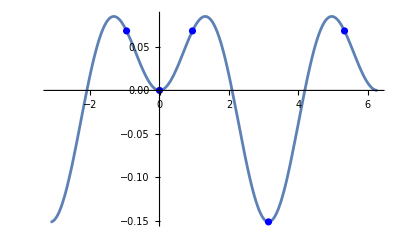

```mathematica
Block[{px=0., py=0., fc=testfieldconfigNo3, saddles, tc=testtargetconfig},
saddles=findSaddles[fc,tc][px,py];
Show[{
Plot[fieldFromConfig[fc][ωt],{ωt,-π,2π}],
ListPlot[{Re[#],fieldFromConfig[fc][Re[#]]}&/@saddles,PlotStyle->Blue]
(*,ListPlot[{Re[#],fieldFromConfig[testfieldconfig1][Re[#]]}&/@findSaddles[testfieldconfig1,testtargetconfig][4],PlotStyle->Red]*)
}]
]
```

```mathematica
DynamicModule[{fc=testfieldconfigNo3, saddles, tc=testtargetconfig},
Manipulate[
saddles=findSaddles[fc,tc][px,py];
Show[{
ListLinePlot3D[Table[{ωt,fieldFromConfig[fc][ωt],field2fromConfig[fc][ωt]},{ωt,-π+0.5,2π-0.5,.1}]],
ListPointPlot3D[{Re[#],fieldFromConfig[fc][Re[#]],field2fromConfig[fc][Re[#]]}&/@saddles,PlotStyle->Blue]
}]
,{px,-3,+3} ,{py,-3,+3}]
]
```

```mathematica
DynamicModule[{fc=testfieldconfigNo3, saddles, tc=testtargetconfig},
Manipulate[
saddles=findgloopySaddles[fc,tc][px,py];
Show[{
ListLinePlot3D[Table[{ωt,fieldFromConfig[fc][ωt],field2fromConfig[fc][ωt]},{ωt,-π+0.5,2π-0.5,.1}]],
ListPointPlot3D[{Re[#],fieldFromConfig[fc][Re[#]],field2fromConfig[fc][Re[#]]}&/@saddles,PlotStyle->Blue]
}]
,{px,-3,+3} ,{py,-3,+3}]
]
findωtBorder[testfieldconfigNo3]
```

2.0944

### Classifying saddle points

#### ClassifySaddles[]

```mathematica
classifygloops[fieldConfig_,targetConfig_][saddlesList_,gloopList_]:=Module[{
saddles,gloops,
ABCsaddles,Agloop,Bgloop,Cgloop,
ABCsaddlesclassified,Dsaddle,Dgloop,
classifiedsaddles,classifiedgloops,
ωtmin,ωtborder,nsaddles1cycle,
myπ
},

ωtborder=findωtBorder[fieldConfig];

saddles=SortBy[saddlesList,Round[{Abs[Re[#]],Abs[Im[#]]},0.0001]&];
gloops=SortBy[gloopList,Round[{Abs[Re[#]],Abs[Im[#]]},0.0001]&];

nsaddles1cycle=Length[
Select[saddles,-π<Re[#]<=π&]
];

(*Print["nsaddles1cycle: ",nsaddles1cycle];*)

Which[
nsaddles1cycle>3,(*if there're more than three saddles within one cycle*)
Block[{ACsaddles},
ABCsaddles=SortBy[saddles[[1;;3]],Round[{Im[#],-Abs[Re[#]]},10^-5]&];
ACsaddles=SortBy[ABCsaddles[[1;;2]],Round[{Re[#],Im[#]},10^-5]&];
Agloop=Nearest[gloops,ACsaddles[[1]]];
Bgloop=Nearest[gloops,ABCsaddles[[3]]];
Cgloop=Nearest[gloops,ACsaddles[[2]]];
(*Print["ACSaddles: ",ACsaddles];*)

],

nsaddles1cycle<3,
Print["You're trying to classifying less than three saddle points, who knows how to do that!?!"];
,

nsaddles1cycle==3,
ABCsaddlesclassified={
{saddles[[1]],"A"},{saddles[[1]],"C"},
{saddles[[2]],"B"} };
Agloop=Nearest[gloops,saddles[[1]]];
Bgloop=Nearest[gloops,saddles[[2]]];
Cgloop=Nearest[gloops,saddles[[1]]];
];


Dsaddle=Select[saddles[[Min[nsaddles1cycle,4];;-1]],ωtborder<Re[#]&][[1]];
Dgloop=Nearest[gloops,Dsaddle];


classifiedgloops=SortBy[
Join[
{{Agloop,"A"}},
{{Bgloop,"B"}},
{{Cgloop,"C"}},
{{Dgloop,"D"}}
],Re[#[[1]]]&]

]
classifySaddles[fieldConfig_,targetConfig_][saddlesList_]:=Module[{
saddles,
ABCsaddles,
ABCsaddlesclassified,Dsaddle,
classifiedsaddles,
ωtmin,ωtborder,nsaddles1cycle,
myπ
},

ωtborder=findωtBorder[fieldConfig];

saddles=SortBy[saddlesList,Round[{Abs[Re[#]],Abs[Im[#]]},0.0001]&];


nsaddles1cycle=Length[
Select[saddles,-π<Re[#]<=π&]
];

(*Print["nsaddles1cycle: ",nsaddles1cycle];*)

Which[
nsaddles1cycle>3,(*if there're more than three saddles within one cycle*)
Block[{ACsaddles},
ABCsaddles=SortBy[saddles[[1;;3]],Round[{Im[#],-Abs[Re[#]]},10^-5]&];
ACsaddles=SortBy[ABCsaddles[[1;;2]],Round[{Re[#],Im[#]},10^-5]&];

(*Print["ACSaddles: ",ACsaddles];*)
ABCsaddlesclassified= Join[
{{ABCsaddles[[3]],"B"}},
{{ACsaddles[[1]],"A"}},
{{ACsaddles[[2]],"C"}} 
]

],

nsaddles1cycle<3,
Print["You're trying to classifying less than three saddle points, who knows how to do that!?!"];
,

nsaddles1cycle==3,
ABCsaddlesclassified={
{saddles[[1]],"A"},{saddles[[1]],"C"},
{saddles[[2]],"B"} }
];


Dsaddle=Select[saddles[[Min[nsaddles1cycle,4];;-1]],ωtborder<Re[#]&][[1]];
classifiedsaddles=SortBy[
Join[
ABCsaddlesclassified,
{{Dsaddle,"D"}}
],Re[#[[1]]]&]

]
δSaddles[fieldConfig_,targetConfig_][saddlesList_,glooplist_]:=Module[{
saddles,gloops,
ABCsaddles,Agloop,Bgloop,Cgloop,
ABCsaddlesclassified,Dsaddle,Dgloop,
classifiedsaddles,
ωtmin,ωtborder,nsaddles1cycle,
δA,δB,δC,δD,deltas,
myπ
},

ωtborder=findωtBorder[fieldConfig];

saddles=SortBy[saddlesList,Round[{Abs[Re[#]],Abs[Im[#]]},0.0001]&];
gloops=SortBy[glooplist,Round[{Abs[Re[#]],Abs[Im[#]]},0.0001]&];
nsaddles1cycle=Length[
Select[saddles,-π<Re[#]<=π&]
];

(*Print["nsaddles1cycle: ",nsaddles1cycle];*)

Which[
nsaddles1cycle>3,(*if there're more than three saddles within one cycle*)
Block[{ACsaddles},
ABCsaddles=SortBy[saddles[[1;;3]],Round[{Im[#],-Abs[Re[#]]},10^-5]&];
ACsaddles=SortBy[ABCsaddles[[1;;2]],Round[{Re[#],Im[#]},10^-5]&];

Agloop=Nearest[gloops,ACsaddles[[1]]];
Bgloop=Nearest[gloops,ABCsaddles[[3]]];
Cgloop=Nearest[gloops,ACsaddles[[2]]];

δA=Agloop-ACsaddles[[1]];
δB=Bgloop-ABCsaddles[[3]];
δC=Cgloop-ACsaddles[[2]];

(*Print["ACSaddles: ",ACsaddles];*)

],

nsaddles1cycle<3,
Print["You're trying to classifying less than three saddle points, who knows how to do that!?!"];
,

nsaddles1cycle==3,
ABCsaddlesclassified={
{saddles[[1]],"A"},{saddles[[1]],"C"},
{saddles[[2]],"B"} };

Agloop=Nearest[gloops,saddles[[1]]];
Bgloop=Nearest[gloops,saddles[[2]]];
Cgloop=Nearest[gloops,saddles[[1]]];

δA=Agloop-saddles[[1]];
δB=Bgloop-saddles[[2]];
δC=Cgloop-saddles[[1]];
];

Dsaddle=Select[saddles[[Min[nsaddles1cycle,4];;-1]],ωtborder<Re[#]&][[1]];
Dgloop=Nearest[gloops,Dsaddle];

δD=Dgloop-Dsaddle;

deltas=
Join[
{{δA,"A"}},
{{δB,"B"}},
{{δC,"C"}},
{{δD,"D"}}
]
]

(*classifygloops[fieldConfig_,targetConfig_][gloopList_]:=Module[{
gloops,
ABCgloops,
ABCgloopsclassified,Dgloop,
classifiedgloops,
ωtmin,ωtborder,ngloops1cycle,
increasing, myπ
},

ωtborder=findωtBorder[fieldConfig];

gloops=SortBy[gloopList,Round[{Abs[Re[#]],Abs[Im[#]]},0.0001]&];

ngloops1cycle=Length[
Select[gloops,-π<Re[#]<=π&]
];



]*)
```

```mathematica
Block[{px=-2,py=2., fc=testfieldconfigNo3, saddles, tc=testtargetconfig},
saddles=findSaddles[fc,tc][px,py];
classifySaddles[fc,tc][saddles]
]
Block[{px=-2,py=2, fc=testfieldconfigNo3, saddles, gloopysaddles,tc=testtargetconfig},
saddles=findSaddles[fc,tc][px,py];
gloopysaddles=findgloopySaddles[fc,tc][px,py];
classifygloops[fc,tc][saddles,gloopysaddles]
]
Block[{px=-2,py=2, fc=testfieldconfigNo3, saddles, gloopysaddles,tc=testtargetconfig},
saddles=findSaddles[fc,tc][px,py];
gloopysaddles=findgloopySaddles[fc,tc][px,py];
δSaddles[fc,tc][saddles,gloopysaddles]
]
```

{{0.264003+1.39692 ⅈ,A},{0.264003+1.39692 ⅈ,C},{0.900221+1.25007 ⅈ,B},{3.54924+0.817992 ⅈ,D}}

{{{0.257725+1.03613 ⅈ},A},{{0.257725+1.03613 ⅈ},C},{{0.532274+0.993671 ⅈ},B},{{3.60173+0.687414 ⅈ},D}}

{{{-0.00627739-0.360789 ⅈ},A},{{-0.367947-0.256402 ⅈ},B},{{-0.00627739-0.360789 ⅈ},C},{{0.0524947-0.130578 ⅈ},D}}

#### Colors for labels

```mathematica
LabelColors=<|"A"->Lighter[RGBColor[0.92, 0.16, 0.05],0.15],"B"->RGBColor[0, 0.9, 0.13],"C"->Darker[RGBColor[0, 0.4, 0.875],0.15],"D"->RGBColor[1, 0.9, 0]|>
```

<|A→RGBColor[0.932, 0.28600000000000003, 0.1925],B→RGBColor[0, 0.9, 0.13],C→RGBColor[0., 0.34, 0.74375],D→RGBColor[1, 0.9, 0]|>

### Checking which saddles are relevant

#### actionsForSaddles[]

```mathematica
actionsForSaddles[fieldConfig_,targetConfig_][pp_,pq_]:=
Association[
Apply[
Function[{ωt,label},label->basicActionFromConfig[fieldConfig,targetConfig][pp,pq,ωt]],
classifySaddles[fieldConfig,targetConfig][findSaddles[fieldConfig,targetConfig][pp,pq]] 
,{1}
]
]
gloopyactionsForSaddles[fieldConfig_,targetConfig_][pp_,pq_]:=
Association[
Apply[
Function[{ωt,label},label->actionFromConfig[fieldConfig,targetConfig][pp,pq,ωt]],
classifygloops[fieldConfig,targetConfig][findSaddles[fieldConfig,targetConfig][pp,pq],findgloopySaddles[fieldConfig,targetConfig][pp,pq]] 
,{1}
]
]
δactionforSaddles[fieldConfig_,targetConfig_][pp_,pq_]:=
Association[
Apply[
Function[{ωt,label},label->actionFromConfig[fieldConfig,targetConfig][pp,pq,ωt]],
δSaddles[fieldConfig,targetConfig][findSaddles[fieldConfig,targetConfig][pp,pq],findgloopySaddles[fieldConfig,targetConfig][pp,pq]]
,{1}
]
]
```

#### contributingSaddles[]

```mathematica
contributingSaddles[fieldConfig_,targetConfig_][px_]:=
Module[{actions,myfun},
actions=actionsForSaddles[fieldConfig,targetConfig][px];
myfun=Function[x,Abs[Re[Round[x,10^-5]]]];
(*THIS IS NOT YET CORRECT THOUGHT THROUGH*)
Which[px>0,
Which[
myfun[actions[["C"]]]<myfun[actions[["A"]]],
{"C","D"},
myfun[actions[["C"]]]<myfun[actions[["B"]]],
{"C","B","D"},
myfun[actions[["A"]]]==myfun[actions[["B"]]]==myfun[actions[["C"]]],
{"A","D"},
True,
{"A","B","C","D"}
],
px<0,
Which[
myfun[actions[["A"]]]<myfun[actions[["C"]]],
{"A","D"},
myfun[actions[["A"]]]<myfun[actions[["B"]]],
{"A","B","D"},
myfun[actions[["A"]]]==myfun[actions[["B"]]]==myfun[actions[["C"]]],
{"A","D"},
True,
{"A","B","C","D"}
],
px==0,
Which[
myfun[actions[["A"]]]==myfun[actions[["B"]]]==myfun[actions[["C"]]],
{"A","D"},
True,
{"A","B","C","D"}
],
True,
Print["I think I've got a mistake here"]
]

]
```

```mathematica
contributingSaddles[testfieldconfig,testtargetconfig][3.]//AbsoluteTiming
```

{0.106574,{A,B,C,D}}

## Ionization Yield

### Yield for one single saddle point

#### yield[]

From equation (53) in J Phys 2014 Popruzhenko

```mathematica
yield[fieldConfig_,targetConfig_][saddle_Association]:=Block[{ωtx,ω,px,κ},
{ωtx,px}={#["ωt"],#["p"]}&@saddle;
 ω="ω"/.(Association@@fieldConfig);
κ=κFromConfig[targetConfig];
(
1/2 Sqrt[ (ⅈ κ)/(d2Sdωt2[fieldConfig,targetConfig][px,ωtx] ω)] 
×Ckl × Ylm
×Exp[ⅈ actionFromConfig[fie ldConfig,targetConfig][px,ωtx]/ω ]
)/.{Ckl->1, Ylm->Sqrt[1/(4π)]}  (*Ckl is a dimensionless asymptotic and can be taken to be 1 for Hydrogen*)

]
```

```mathematica
SphericalHarmonicY[0,0,theta,r]
```

1/(2 √π)

p = potA[ωt0] : drift momentum (measured at the detector), for non-zero velocity at ionization, use: p=potA[ωt0] +v0

### for a given p, get all saddles’ yields

```mathematica
yieldsPerSaddles[fieldConfig_,targetConfig_][px_]:=Module[{saddles,data,contributors},
(*find and classify saddles*)
saddles=<|"label"->#[[2]],"p"->px,"ωt"->#[[1]]|>&/@classifySaddles[fieldConfig,targetConfig][findSaddles[fieldConfig,targetConfig][px]];
(*add each saddles' contribution to that dictionary*)
data=Append[#,"yield"->Quiet@yield[fieldConfig,targetConfig][#]]&/@saddles;
(*check which saddles are contributing and add that info to the dictionary as well*)
contributors=contributingSaddles[fieldConfig,targetConfig][px];
SortBy[(Append[#,"contributing"->MemberQ[contributors,#["label"]]]&/@data),#[["label"]]&]
]
```

```mathematica
yieldsPerSaddles[testfieldconfig,testtargetconfig][0.5]
```

{<|label→A,p→0.5,ωt→-1.16273+1.7713 ⅈ,yield→-1.65609×10^-8-1.0656×10^-8 ⅈ,contributing→True|>,<|label→B,p→0.5,ωt→-0.193553+1.89477 ⅈ,yield→-6.49415×10^-9-2.65414×10^-9 ⅈ,contributing→True|>,<|label→C,p→0.5,ωt→1.6224+1.68205 ⅈ,yield→3.61223×10^-7+2.84325×10^-7 ⅈ,contributing→True|>,<|label→D,p→0.5,ωt→2.87548+1.55857 ⅈ,yield→-1.24894×10^-6+1.15913×10^-7 ⅈ,contributing→True|>}

### Summing contributions from contributing saddles

```mathematica
totalYield[yieldsS_List]:=Total[#["yield"]&/@Select[yieldsS,#["contributing"]&]]
```

## Test: Calculate a whole spectrum (for a given fieldconfig and targetconfig)

#### 0) Define your field configuration and target configuration

for example this:

```mathematica
fcTWOB=makeTWOBFieldConfig["E0"->Sqrt[4×10^14/(3.5×10^16)],(*4×10^14 is the intensity in W/cm^2*)
"ω"->λToω[800]](*800 nm wavelength*)
```

fieldConfig[E1→0.0755929,E2→0.0755929,E0→0.106904,ϕ1→π/2,ϕ2→-π/2,r→1,s→2,ω→0.0569395]

```mathematica
target=targetConfig["Ip"->0.5];
```

#### 1) Define pvalues

Note: What is a good range for the values of momentum?

```mathematica
pvalues=Range[-3,3,0.01];
```

#### 2) Get data (this might take a bit)

Tipp #1: use ParallelTable instead Table once you’re sure the code works.
Tipp #2: In case it goes wrong, abort calculations with “Alt” + ”.”

```mathematica
spectrumdata=Block[{fc=fcTWOB,tc=target},
Table[yieldsPerSaddles[fc,tc][px],{px,pvalues}]
]
```

{{<|label→A,p→-3.,ωt→-2.10957+2.18151 ⅈ,yield→-1.94322×10^-53-1.29713×10^-53 ⅈ,contributing→True|>,<|label→B,p→-3.,ωt→0.563723+2.33115 ⅈ,yield→1.10126×10^-67-1.40748×10^-67 ⅈ,contributing→True|>,<|label→C,p→-3.,ωt→0.860905+2.30802 ⅈ,yield→1.90978×10^-67-8.21909×10^-68 ⅈ,contributing→True|>,<|label→D,p→-3.,ωt→3.82654+2.15838 ⅈ,yield→-2.03197×10^-53+1.79083×10^-53 ⅈ,contributing→True|>},599,{1}}
 |  |  |  |

$OutputSizeLimit::nosess: This output can only be updated in the same kernel session that generated it.

#### 3) Calculate the total yield (i.e., summing over all contributions)

```mathematica
totalspectrumdata=Table[<|"p"->pvalues[[i]],"totalYield"->totalYield[spectrumdata[[i]]]|>,{i,1, Length@pvalues}];
```

#### 4) Plotting the spectrum and each individual contribution

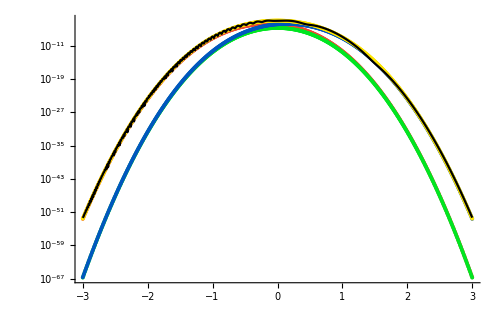

```mathematica
Block[{datalabel},
Show[{
Table[ (*for each label*)
(*extract the data for the respective label from the list*)
datalabel=Function[datap,Select[datap,#["label"]==label &]]/@spectrumdata;

ListLogPlot[{#[[1]]["p"],Abs[#[[1]]["yield"]]}&/@ (*plot (p,yield)*)
datalabel, 
PlotStyle->Directive[LabelColors[label],Thick],Joined->False]

,{label,{"A","B","C","D"}}],

(*plot the total yield as well*)
ListLogPlot[{#["p"],Abs[#["totalYield"]]}&/@totalspectrumdata,PlotStyle->Black,Joined->True]
}
,ImageSize->500
,AxesOrigin->{0,Log[0.001]}
,PlotRange->{Automatic,{Log[10^-30],Automatic}}
]]
```